```mathematica
G1[a_,x_]:=(1+3*a/(2*Pi-3*a)*Cos[x])/(2*Pi)
G2[a_,x_,b_,x0_]:=(Exp[-(x-x0)^2/(b*Pi)]+Exp[-(x+x0)^2/(b*Pi)])/(√b π (Erf[(π-x0)/(√b √π)]+Erf[(π+x0)/(√b √π)]))
bb[x_]:=m*(x-x0)+y0;
bbb[x_]:=(0.05-1)/(90-60)*180/Pi*(x-Pi/3)+1;
G3[a_,x_]:=(Exp[-(x-2*(a-Pi/3))^2/(bb[a]*Pi)]+Exp[-(x+2*(a-Pi/3))^2/(bb[a]*Pi)])/(-π √(a m-m x0+y0) (Erf[(6 a-5 π)/(3 √π √(a m-m x0+y0))]-Erf[(6 a+π)/(3 √π √(a m-m x0+y0))]))/.{m->(0.05-1)/(90-60)*180/Pi,x0->Pi/3,y0->1}
```

```mathematica
FullSimplify[-(x-x0)^2*b-(x+x0)^2*b]
```

-2 b (x^2+x0^2)

```mathematica
bb[Pi/2]
```

0.1

```mathematica
Integrate[G1[a,x],{x,-Pi,Pi}]
```

1

```mathematica
FullSimplify[Integrate[G2[a,x,b,x0],{x,-Pi,Pi}]]
```

1

```mathematica
FullSimplify[Integrate[(Exp[-(x-2*(a-a0))^2/(b*Pi)]+Exp[-(x+2*(a-a0))^2/(b*Pi)]),{x,-Pi+B,Pi-B}]]
```

1/2 √b π (-Erf[(2 a-2 a0+B-π)/(√b √π)]-Erf[(-2 a+2 a0+B-π)/(√b √π)]+Erf[(2 a-2 a0-B+π)/(√b √π)]+Erf[(-2 a+2 a0-B+π)/(√b √π)])

```mathematica
FullSimplify[Integrate[(Exp[-(x-2*(a-a0))^2/(b*Pi)]+Exp[-(x+2*(a-a0))^2/(b*Pi)]),{x,-Pi,Pi}]]
```

√b π (Erf[(2 a-2 a0+π)/(√b √π)]+Erf[(-2 a+2 a0+π)/(√b √π)])

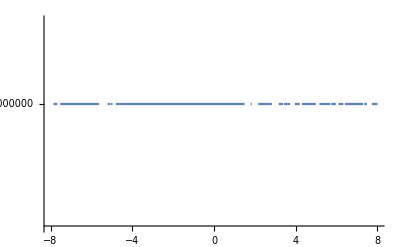

```mathematica
Plot[%330,{a,-8,8}]
```

```mathematica
FullSimplify[Integrate[(Exp[-(x-2*(a-Pi/3))^2/(b*Pi)]+Exp[-(x+2*(a-Pi/3))^2/(b*Pi)]),{x,-Pi,Pi}]]
```

√b π (-Erf[(6 a-5 π)/(3 √b √π)]+Erf[(6 a+π)/(3 √b √π)])

```mathematica
Manipulate[Plot[{G1[Pi/3,x*Pi/180],G2[a,x*Pi/180,b,(x0)*Pi/180]},{x,0,180}],{a,Pi/3,Pi/2},{b,0.05,10},{x0,0,30}]
```

```mathematica
N[1/Pi]
```

0.31831

```mathematica
Manipulate[Plot[{G1[Pi/3,x*Pi/180],G3[a*Pi/180,x*Pi/180]},{x,0,180}],{a,60,90},{b,0.05,10},{x0,0,30}]
```

```mathematica
Normal[Series[Beta[1/a+1,a+1],{a,Infinity,3}]]
Normal[Series[Beta[b+1,1/b+1],{b,Infinity,3}]]
```

1/a+1/a^2(-1-EulerGamma-Log[a])+1/(12 a^3)(-6+12 EulerGamma+6 EulerGamma^2+π^2+12 Log[a]+12 EulerGamma Log[a]+6 Log[a]^2)

```mathematica
FullSimplify[-6+12 EulerGamma+6 EulerGamma^2+π^2+12 Log[a]+12 EulerGamma Log[a]+6 Log[a]^2]
```

-6+6 EulerGamma (2+EulerGamma)+π^2+6 Log[a] (2+2 EulerGamma+Log[a])

```mathematica
N[EulerGamma]
```

0.577216

```mathematica
NumberForm[0.5772156649015329,16]
```

0.5772156649015328

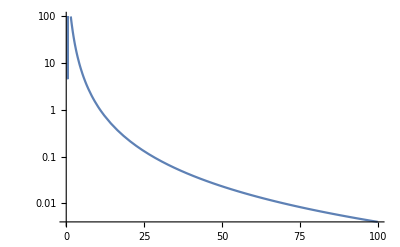

```mathematica
LogPlot[{100*Abs[(1/a+(-1-EulerGamma-Log[a])/a^2+1/(12 a^3)(-6+12 EulerGamma+6 EulerGamma^2+π^2+12 Log[a]+12 EulerGamma Log[a]+6 Log[a]^2)-Beta[1/a+1,a+1])/Beta[1/a+1,a+1]]},{a,0.1,100},PlotRange->{0,100}]
```

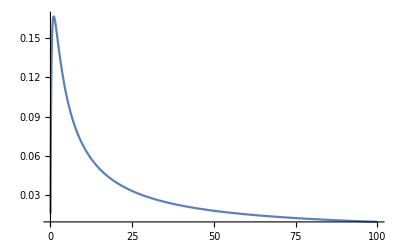

```mathematica
Plot[Beta[1/a+1,a+1],{a,0.01, 100},PlotRange->All]
```

```mathematica
N[100*Abs[(1/a+(-1-EulerGamma-Log[a])/a^2+1/(12 a^3)(-6+12 EulerGamma+6 EulerGamma^2+π^2+12 Log[a]+12 EulerGamma Log[a]+6 Log[a]^2)-Beta[1/a+1,a+1])/Beta[1/a+1,a+1]]/.a->15]
```

0.460414